```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
FileNames[]
```

{alignment_processing.nb,eda.m,imgroup.m,neuralalignment.m,prepoc.m}

```mathematica
branches=Import["../output/branches.csv"];
middles = Import["../output/middles.csv"];
ends = Import["../output/ends.csv"];
relNeighbours={{1,0},{0,1},{1,1},{-1,0},{0,-1},{-1,1},{1,-1},{-1,-1}};
```

```mathematica
candidates=Join[middles,ends,branches];
starts=Join[ends,branches];
```

```mathematica
FindNeighboursInCandidates[pos_]:=Flatten[Select[candidates,Function[x,x==#]]&/@(pos+#&/@relNeighbours),1];
```

```mathematica
candidates=Join[middles,ends,branches];
starts=Join[ends,middles];
lines={};
While[starts≠{},
pos=First[starts];
starts = starts/.{pos->Nothing};
candidates=candidates/.{pos->Nothing};
line={pos};
neighbour=pos;
While[neighbour≠{},
neighbours=FindNeighboursInCandidates[neighbour];
neighbour=If[neighbours≠{},First[neighbours],{}];
candidates=candidates/.{neighbour->Nothing};
starts=starts/.{neighbour->Nothing};
AppendTo[line,neighbour];
];
AppendTo[lines,Drop[line,-1]];
]
```

```mathematica
timeStamp[lst_]:=Module[{var=Length[lst]},
Table[{i/(var-1),lst[[i+1]]},{i,0,var-1}]
]
```

```mathematica
filteredLines=Select[lines,Length[#]≠1&];
timeStampedLines=timeStamp/@filteredLines;
```

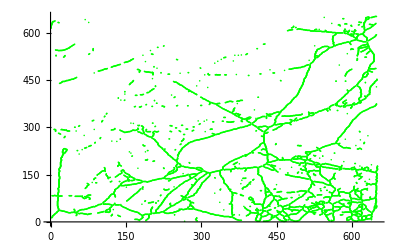

Part::partd: Part specification filteredLines⟦1⟧ is longer than depth of object.

ListPlot::lpn: {{},{{1.,Interpolation[timeStampedLines⟦1⟧][0.]}},{}} is not a list of numbers or pairs of numbers.

```mathematica
middleShow=ListPlot[middles,PlotStyle->Green]
Manipulate[
ListPlot[
{filteredLines[[n]],{Quiet[Interpolation[timeStampedLines[[n]]]][t]},ends}
,PlotStyle->Large],
{t,0,1},{n,1,Length[filteredLines],1}]
```

```mathematica
f=Interpolation[timeStampedLines[[1]]];
```

```mathematica
g[t]:=1;
```

```mathematica
Total[Table[
f=Interpolation[timeStampedLines[[m]]];
fd=D[f[t],t];
NIntegrate[Sqrt[fd.fd],{t,0,1}]
,{m,1,Length[filteredLines]}]]
```

```mathematica
angle[x_,k_]:=If[Abs[ArcCos[x.{0,1}]]<k,1,0]
Total[ParallelTable[
f=Interpolation[timeStampedLines[[m]]];
fd=D[f[t],t];
NIntegrate[angle[f[t]/(f[t].f[t]),π/6]*Sqrt[fd.fd],{t,0,1},Method->"MonteCarlo"]
,{m,1,Length[filteredLines]}]]
```

```mathematica
angle[x_,k_]:=If[Abs[ArcCos[x.{1,0}]]<k,1,0]
Total[Table[
f=Interpolation[timeStampedLines[[m]]];
fd=D[f[t],t];
NIntegrate[angle[f[t]/(f[t].f[t]),π/6]*Sqrt[fd.fd],{t,0,1}]
,{m,1,Length[filteredLines]}]]
```